```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/CaCO3/Common_Tangent-Mathematica/TEST/Files_Outputs"]
oneDat=Import["vol_Free_allTemps_ordered_I.dat"];
twoDat=Import["vol_Free_allTemps_ordered_II.dat"];
temps=Flatten@Import["temperatures.dat"]
```

/Volumes/MicroSD/2_PostDoc_SD/CaCO3/Common_Tangent-Mathematica/TEST/Files_Outputs

{10.,30.1,50.2,70.3,90.4,110.51,130.61,150.71,170.81,190.91,211.01,231.11,251.21,271.31,291.41,311.52,331.62,351.72,371.82,391.92,412.02,432.12,452.22,472.32,492.42,512.53,532.63,552.73,572.83,592.93}

```mathematica
(*30 temperatures. Each 11 for I*)
```

```mathematica
oneDataParts=Table[Partition[oneDat,11][[i]],{i,1,30}];
twoDataParts=Table[Partition[twoDat,9][[i]],{i,1,30}];
```

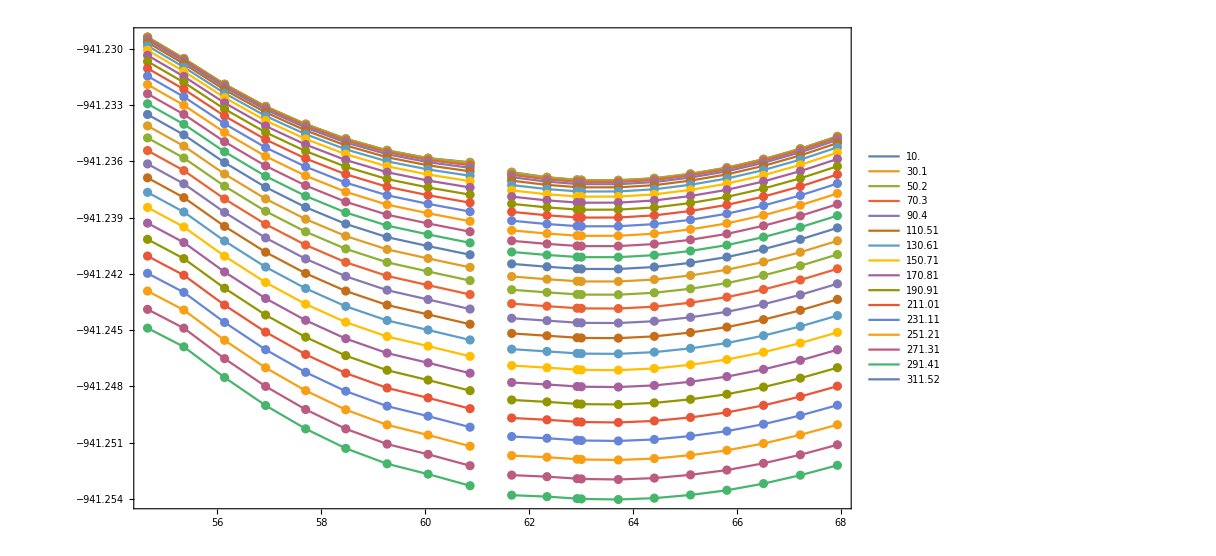

```mathematica
With[{p=30},Show[{ListLinePlot[Evaluate@Table[oneDataParts[[i]],{i,1,p}],PlotLegends->temps],ListPlot[Evaluate@Table[oneDataParts[[i]],{i,1,p}]],ListLinePlot[Evaluate@Table[twoDataParts[[i]],{i,1,p}]],ListPlot[Evaluate@Table[twoDataParts[[i]],{i,1,p}]]},PlotRange->All,Frame->True,ImageSize->900]]
```

```mathematica
fitOneDatx=Table[Fit[oneDataParts[[i]],{1,x,x^2,x^3},x],{i,1,30}];
fitTwoDatx=Table[Fit[twoDataParts[[i]],{1,x,x^2,x^3},x],{i,1,30}];
fitOneDat=fitOneDatx/.x->y;
fitTwoDat=fitTwoDatx/.x->z;
```

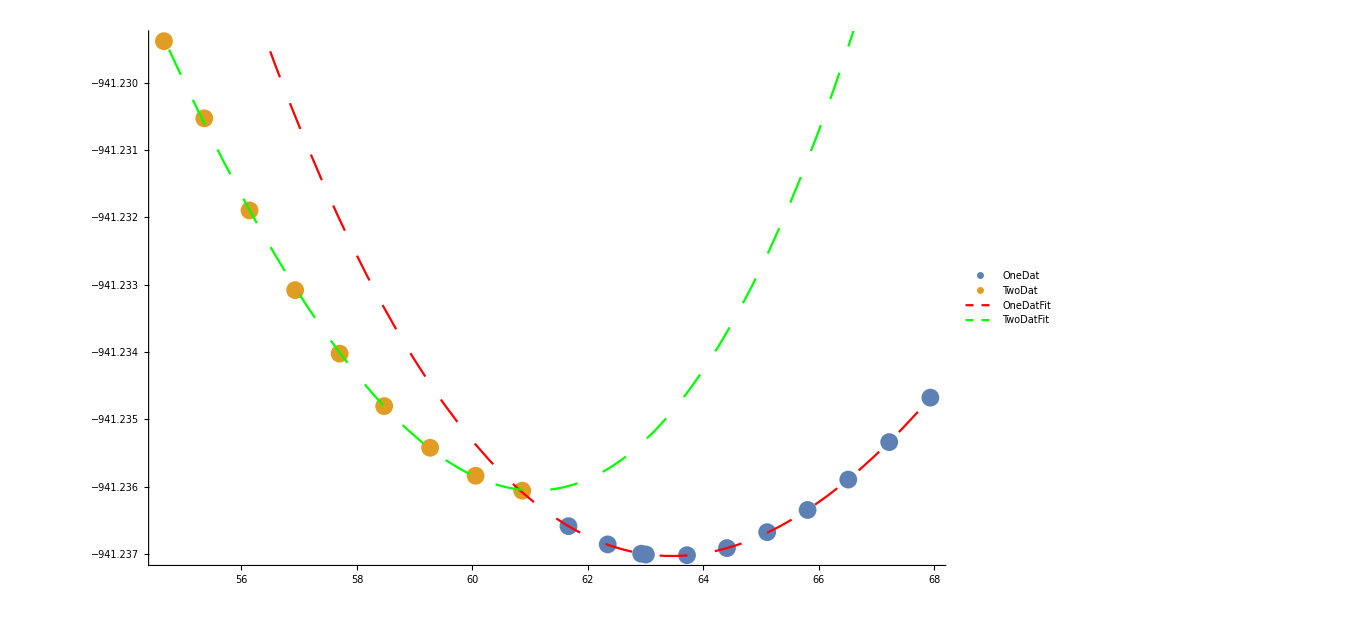

```mathematica
Show[ListPlot[{oneDataParts[[1]],twoDataParts[[1]]},PlotLegends->{"OneDat","TwoDat"}],Plot[fitOneDatx[[1]],{x,55,68},PlotStyle->Directive[Dashing[0.02],Red],PlotLegends->{"OneDatFit"}],Plot[fitTwoDatx[[1]],{x,54,68},PlotStyle->Directive[Dashing[0.02],Green],PlotLegends->{"TwoDatFit"}],ImageSize->1000]
```

```mathematica
fitOneDat
fitOneDatDash=D[fitOneDat,y]
fitTwoDat
fitTwoDatDash=D[fitTwoDat,z]
```

{-939.867-0.0563916 y+0.000756843 y^2-3.28316×10^-6 y^3,-939.913-0.0543148 y+0.000725284 y^2-3.12331×10^-6 y^3,-939.97-0.0517217 y+0.000686071 y^2-2.92559×10^-6 y^3,-940.028-0.0490838 y+0.000646307 y^2-2.72575×10^-6 y^3,-940.087-0.0464632 y+0.000606878 y^2-2.52805×10^-6 y^3,-940.144-0.0438599 y+0.000567745 y^2-2.33208×10^-6 y^3,-940.202-0.0412698 y+0.000528817 y^2-2.13727×10^-6 y^3,-940.259-0.03869 y+0.000490041 y^2-1.94327×10^-6 y^3,-940.317-0.0361186 y+0.000451384 y^2-1.74988×10^-6 y^3,-940.374-0.0335542 y+0.000412822 y^2-1.55696×10^-6 y^3,-940.431-0.0309954 y+0.000374336 y^2-1.36441×10^-6 y^3,-940.488-0.0284412 y+0.00033591 y^2-1.17215×10^-6 y^3,-940.545-0.0258906 y+0.00029753 y^2-9.80099×10^-7 y^3,-940.602-0.0233428 y+0.000259187 y^2-7.88215×10^-7 y^3,-940.658-0.0207973 y+0.00022087 y^2-5.96448×10^-7 y^3,-940.715-0.0182534 y+0.000182572 y^2-4.04765×10^-7 y^3,-940.772-0.0157108 y+0.000144288 y^2-2.13134×10^-7 y^3,-940.829-0.013169 y+0.000106013 y^2-2.15343×10^-8 y^3,-940.886-0.0106279 y+0.0000677425 y^2+1.70054×10^-7 y^3,-940.943-0.00808717 y+0.000029474 y^2+3.61643×10^-7 y^3,-940.999-0.00554665 y-8.79497×10^-6 y^2+5.53246×10^-7 y^3,-941.056-0.00300622 y-0.0000470661 y^2+7.4487×10^-7 y^3,-941.113-0.000465769 y-0.0000853407 y^2+9.3652×10^-7 y^3,-941.17+0.00207479 y-0.00012362 y^2+1.1282×10^-6 y^3,-941.227+0.00461551 y-0.000161904 y^2+1.31992×10^-6 y^3,-941.284+0.00715644 y-0.000200194 y^2+1.51167×10^-6 y^3,-941.341+0.00969761 y-0.00023849 y^2+1.70346×10^-6 y^3,-941.398+0.012239 y-0.000276792 y^2+1.89529×10^-6 y^3,-941.455+0.0147808 y-0.000315101 y^2+2.08716×10^-6 y^3,-941.512+0.0173228 y-0.000353416 y^2+2.27907×10^-6 y^3}

{-0.0563916+0.00151369 y-9.84947×10^-6 y^2,-0.0543148+0.00145057 y-9.36994×10^-6 y^2,-0.0517217+0.00137214 y-8.77678×10^-6 y^2,-0.0490838+0.00129261 y-8.17725×10^-6 y^2,-0.0464632+0.00121376 y-7.58415×10^-6 y^2,-0.0438599+0.00113549 y-6.99625×10^-6 y^2,-0.0412698+0.00105763 y-6.41182×10^-6 y^2,-0.03869+0.000980082 y-5.82982×10^-6 y^2,-0.0361186+0.000902768 y-5.24965×10^-6 y^2,-0.0335542+0.000825644 y-4.67089×10^-6 y^2,-0.0309954+0.000748672 y-4.09324×10^-6 y^2,-0.0284412+0.00067182 y-3.51644×10^-6 y^2,-0.0258906+0.000595061 y-2.9403×10^-6 y^2,-0.0233428+0.000518374 y-2.36464×10^-6 y^2,-0.0207973+0.00044174 y-1.78935×10^-6 y^2,-0.0182534+0.000365145 y-1.21429×10^-6 y^2,-0.0157108+0.000288577 y-6.39403×10^-7 y^2,-0.013169+0.000212026 y-6.46029×10^-8 y^2,-0.0106279+0.000135485 y+5.10161×10^-7 y^2,-0.00808717+0.0000589479 y+1.08493×10^-6 y^2,-0.00554665-0.0000175899 y+1.65974×10^-6 y^2,-0.00300622-0.0000941321 y+2.23461×10^-6 y^2,-0.000465769-0.000170681 y+2.80956×10^-6 y^2,0.00207479-0.00024724 y+3.38461×10^-6 y^2,0.00461551-0.000323808 y+3.95976×10^-6 y^2,0.00715644-0.000400388 y+4.53502×10^-6 y^2,0.00969761-0.00047698 y+5.11039×10^-6 y^2,0.012239-0.000553585 y+5.68588×10^-6 y^2,0.0147808-0.000630202 y+6.26148×10^-6 y^2,0.0173228-0.000706831 y+6.8372×10^-6 y^2}

{-941.696+0.0345721 z-0.000761722 z^2+5.22473×10^-6 z^3,-941.628+0.0309551 z-0.000698302 z^2+4.85419×10^-6 z^3,-941.556+0.0271721 z-0.000631808 z^2+4.46456×10^-6 z^3,-941.504+0.0244036 z-0.000582947 z^2+4.17682×10^-6 z^3,-941.475+0.0228477 z-0.000555223 z^2+4.01166×10^-6 z^3,-941.468+0.0224671 z-0.000547997 z^2+3.96549×10^-6 z^3,-941.481+0.0231085 z-0.000558597 z^2+4.02281×10^-6 z^3,-941.51+0.0245913 z-0.000583878 z^2+4.16538×10^-6 z^3,-941.552+0.0267519 z-0.000620982 z^2+4.37661×10^-6 z^3,-941.604+0.0294557 z-0.000667562 z^2+4.64287×10^-6 z^3,-941.665+0.0325962 z-0.000721764 z^2+4.9534×10^-6 z^3,-941.733+0.0360908 z-0.000782144 z^2+5.29981×10^-6 z^3,-941.806+0.039875 z-0.00084758 z^2+5.67561×10^-6 z^3,-941.884+0.0438988 z-0.000917197 z^2+6.07569×10^-6 z^3,-941.965+0.0481226 z-0.000990305 z^2+6.49606×10^-6 z^3,-942.05+0.0525151 z-0.00106636 z^2+6.93355×10^-6 z^3,-942.138+0.0570511 z-0.00114492 z^2+7.38562×10^-6 z^3,-942.228+0.0617103 z-0.00122563 z^2+7.8502×10^-6 z^3,-942.32+0.0664761 z-0.00130821 z^2+8.32561×10^-6 z^3,-942.414+0.0713347 z-0.00139241 z^2+8.81047×10^-6 z^3,-942.509+0.0762749 z-0.00147803 z^2+9.3036×10^-6 z^3,-942.606+0.0812869 z-0.00156491 z^2+9.80406×10^-6 z^3,-942.704+0.0863627 z-0.00165291 z^2+0.000010311 z^3,-942.804+0.0914954 z-0.0017419 z^2+0.0000108237 z^3,-942.904+0.096679 z-0.00183178 z^2+0.0000113416 z^3,-943.005+0.101908 z-0.00192246 z^2+0.0000118642 z^3,-943.107+0.107179 z-0.00201387 z^2+0.000012391 z^3,-943.21+0.112487 z-0.00210593 z^2+0.0000129216 z^3,-943.313+0.11783 z-0.00219859 z^2+0.0000134557 z^3,-943.417+0.123203 z-0.00229179 z^2+0.000013993 z^3}

{0.0345721-0.00152344 z+0.0000156742 z^2,0.0309551-0.0013966 z+0.0000145626 z^2,0.0271721-0.00126362 z+0.0000133937 z^2,0.0244036-0.00116589 z+0.0000125305 z^2,0.0228477-0.00111045 z+0.000012035 z^2,0.0224671-0.00109599 z+0.0000118965 z^2,0.0231085-0.00111719 z+0.0000120684 z^2,0.0245913-0.00116776 z+0.0000124961 z^2,0.0267519-0.00124196 z+0.0000131298 z^2,0.0294557-0.00133512 z+0.0000139286 z^2,0.0325962-0.00144353 z+0.0000148602 z^2,0.0360908-0.00156429 z+0.0000158994 z^2,0.039875-0.00169516 z+0.0000170268 z^2,0.0438988-0.00183439 z+0.0000182271 z^2,0.0481226-0.00198061 z+0.0000194882 z^2,0.0525151-0.00213272 z+0.0000208007 z^2,0.0570511-0.00228984 z+0.0000221569 z^2,0.0617103-0.00245127 z+0.0000235506 z^2,0.0664761-0.00261642 z+0.0000249768 z^2,0.0713347-0.00278482 z+0.0000264314 z^2,0.0762749-0.00295606 z+0.0000279108 z^2,0.0812869-0.00312982 z+0.0000294122 z^2,0.0863627-0.00330581 z+0.000030933 z^2,0.0914954-0.00348379 z+0.0000324712 z^2,0.096679-0.00366356 z+0.0000340249 z^2,0.101908-0.00384492 z+0.0000355927 z^2,0.107179-0.00402774 z+0.0000371731 z^2,0.112487-0.00421186 z+0.0000387649 z^2,0.11783-0.00439718 z+0.0000403672 z^2,0.123203-0.00458358 z+0.000041979 z^2}

```mathematica
sol=Solve[{(fitOneDat[[1]]-fitTwoDat[[1]])/(y-z)==fitTwoDatDash[[1]]&&(fitOneDat[[1]]-fitTwoDat[[1]])/(y-z)==fitOneDatDash[[1]]},{y,z},Reals]
```

```mathematica
solConditions=Table[Solve[{(fitOneDat[[i]]-fitTwoDat[[i]])/(y-z)==fitTwoDatDash[[i]]&&(fitOneDat[[i]]-fitTwoDat[[i]])/(y-z)==fitOneDatDash[[i]]&&56<z<64&&56<y<64},{y,z},Reals],{i,1,30}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{y→60.8027,z→60.8027},{y→61.8282,z→59.8666}},{{y→60.7951,z→60.7951},{y→61.7938,z→59.8806}},{{y→60.7796,z→60.7796},{y→61.7378,z→59.8997}},{{y→60.7591,z→60.7591},{y→61.6727,z→59.9202}},{{y→60.7348,z→60.7348},{y→61.6038,z→59.9393}},{{y→60.7072,z→60.7072},{y→61.5332,z→59.956}},{{y→60.6764,z→60.6764},{y→61.4609,z→59.9694}},{{y→60.6422,z→60.6422},{y→61.3864,z→59.9794}},{{y→60.6043,z→60.6043},{y→61.3083,z→59.9856}},{{y→60.562,z→60.562},{y→61.2252,z→59.9878}},{{y→60.5142,z→60.5142},{y→61.1352,z→59.9854}},{{y→60.4596,z→60.4596},{y→61.0356,z→59.9775}},{{y→60.396,z→60.396},{y→60.9229,z→59.9627}},{{y→60.3195,z→60.3195},{y→60.7913,z→59.9385}},{{y→60.2235,z→60.2235},{y→60.6309,z→59.9004}},{{y→56.6171,z→56.9839},{y→56.8021,z→56.8021},{y→60.093,z→60.093},{y→60.4207,z→59.8377}},{{y→58.0393,z→58.3747},{y→58.2203,z→58.2203},{y→59.8815,z→59.8815},{y→60.0966,z→59.7163}},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
solConditions[[1;;18]]
```

{{{y→60.8027,z→60.8027},{y→61.8282,z→59.8666}},{{y→60.7951,z→60.7951},{y→61.7938,z→59.8806}},{{y→60.7796,z→60.7796},{y→61.7378,z→59.8997}},{{y→60.7591,z→60.7591},{y→61.6727,z→59.9202}},{{y→60.7348,z→60.7348},{y→61.6038,z→59.9393}},{{y→60.7072,z→60.7072},{y→61.5332,z→59.956}},{{y→60.6764,z→60.6764},{y→61.4609,z→59.9694}},{{y→60.6422,z→60.6422},{y→61.3864,z→59.9794}},{{y→60.6043,z→60.6043},{y→61.3083,z→59.9856}},{{y→60.562,z→60.562},{y→61.2252,z→59.9878}},{{y→60.5142,z→60.5142},{y→61.1352,z→59.9854}},{{y→60.4596,z→60.4596},{y→61.0356,z→59.9775}},{{y→60.396,z→60.396},{y→60.9229,z→59.9627}},{{y→60.3195,z→60.3195},{y→60.7913,z→59.9385}},{{y→60.2235,z→60.2235},{y→60.6309,z→59.9004}},{{y→56.6171,z→56.9839},{y→56.8021,z→56.8021},{y→60.093,z→60.093},{y→60.4207,z→59.8377}},{{y→58.0393,z→58.3747},{y→58.2203,z→58.2203},{y→59.8815,z→59.8815},{y→60.0966,z→59.7163}},{}}

```mathematica
solConditions[[1]][[2]]
```

{y→61.8282,z→59.8666}

```mathematica
a=Table[fitTwoDat[[i]]/.solConditions[[i]][[2]],{i,1,17}]
b=Table[-fitOneDatDash[[i]]*z/.solConditions[[i]][[2]],{i,1,17}]
c=Table[(fitOneDatDash[[i]]/.solConditions[[i]][[2]])*x,{i,1,17}]
commonTangent=Table[a[[i]]+b[[i]]+c[[i]],{i,1,17}]
```

{-941.236,-941.236,-941.236,-941.236,-941.236,-941.236,-941.236,-941.237,-941.237,-941.237,-941.238,-941.238,-941.239,-941.239,-941.24,-941.237,-941.24}

{0.0272354,0.0273987,0.0276701,0.0279973,0.0283648,0.0287662,0.0292013,0.0296743,0.0301929,0.0307683,0.0314167,0.0321614,0.0330376,0.0341031,0.0354627,0.081245,0.0627073}

{-0.000454935 x,-0.000457556 x,-0.000461941 x,-0.000467243 x,-0.000473225 x,-0.000479789 x,-0.000486937 x,-0.000494742 x,-0.000503335 x,-0.000512909 x,-0.000523739 x,-0.000536224 x,-0.00055097 x,-0.000568968 x,-0.000592028 x,-0.00143032 x,-0.00107707 x}

{-941.209-0.000454935 x,-941.208-0.000457556 x,-941.208-0.000461941 x,-941.208-0.000467243 x,-941.208-0.000473225 x,-941.207-0.000479789 x,-941.207-0.000486937 x,-941.207-0.000494742 x,-941.207-0.000503335 x,-941.207-0.000512909 x,-941.206-0.000523739 x,-941.206-0.000536224 x,-941.206-0.00055097 x,-941.205-0.000568968 x,-941.204-0.000592028 x,-941.156-0.00143032 x,-941.177-0.00107707 x}

```mathematica
phaseBoundaryData=Transpose[{temps[[1;;17]],(c/.x->-1)*4.3597482*10^3}]
```

{{10.,1.9834},{30.1,1.99483},{50.2,2.01395},{70.3,2.03706},{90.4,2.06314},{110.51,2.09176},{130.61,2.12292},{150.71,2.15695},{170.81,2.19441},{190.91,2.23616},{211.01,2.28337},{231.11,2.3378},{251.21,2.40209},{271.31,2.48056},{291.41,2.58109},{311.52,6.23582},{331.62,4.69575}}

```mathematica
phaseBoundaryData//TableForm
```

10. | 1.9834
30.1 | 1.99483
50.2 | 2.01395
70.3 | 2.03706
90.4 | 2.06314
110.51 | 2.09176
130.61 | 2.12292
150.71 | 2.15695
170.81 | 2.19441
190.91 | 2.23616
211.01 | 2.28337
231.11 | 2.3378
251.21 | 2.40209
271.31 | 2.48056
291.41 | 2.58109
311.52 | 6.23582
331.62 | 4.69575

```mathematica
Export["absolutePressuresMathematica.dat",phaseBoundaryData//TableForm]
```

absolutePressuresMathematica.dat

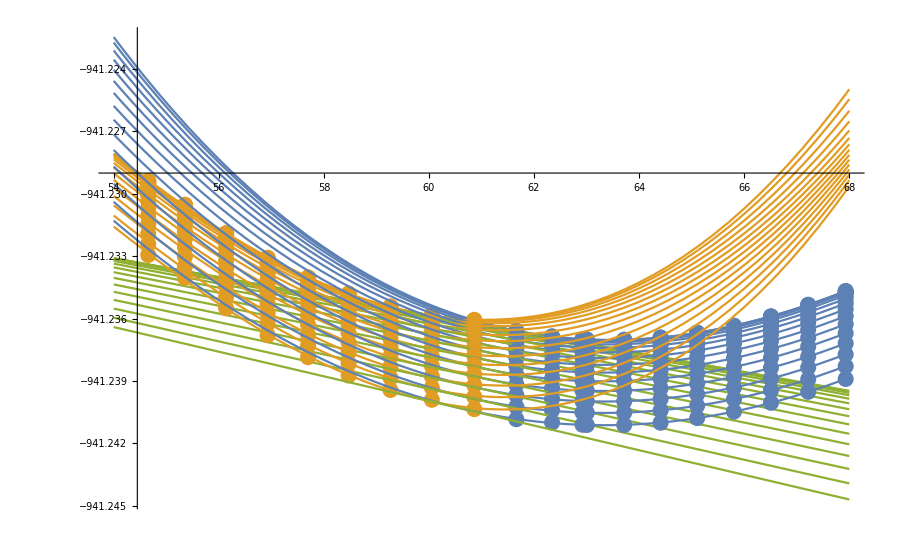

```mathematica
Show[Table[Show[ListPlot[{oneDataParts[[i]],twoDataParts[[i]]}],Plot[{fitOneDatx[[i]],fitTwoDatx[[i]],commonTangent[[i]]},{x,54,68}],ImageSize->900],{i,1,15}],PlotRange->All]
```

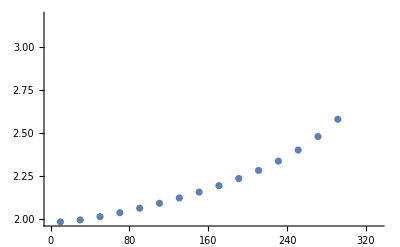

```mathematica
ListPlot@phaseBoundaryData
```